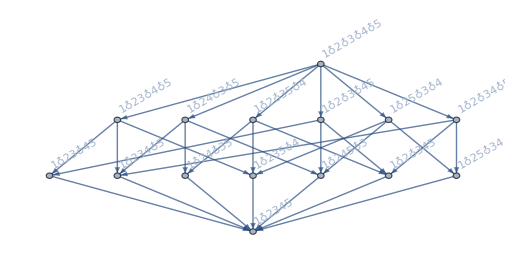
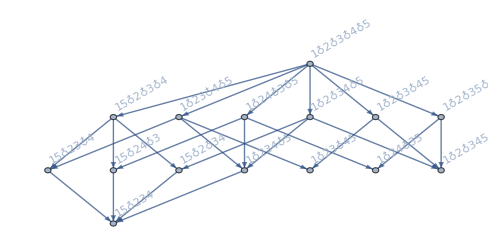
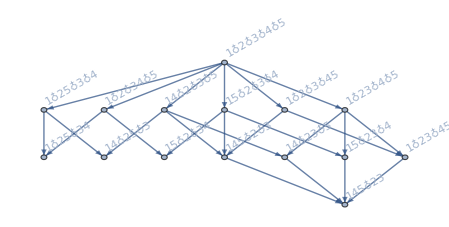
{{-Graphics-,1},{-Graphics-,1},{-Graphics-,1}}

```mathematica
Tally[Map[FormulaGraphReverse2[FindFullFormula[#]]&,Select[ConnectedGraphs[5],TreeGraphQ]],IsomorphicGraphQ]
```

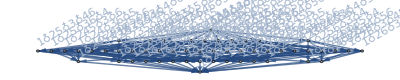
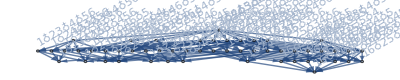
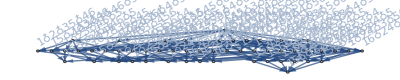
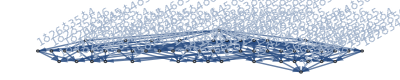
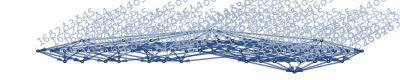
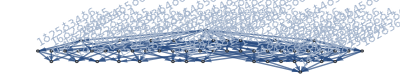
{{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1},{-Graphics-,1}}

```mathematica
Tally[Map[FormulaGraphReverse2[FindFullFormula[#]]&,Select[ConnectedGraphs[6],TreeGraphQ]],IsomorphicGraphQ]
```

```mathematica
Map[Last,Tally[Map[FormulaGraphReverse2[FindFullFormula[#]]&,Select[ConnectedGraphs[7],TreeGraphQ]],IsomorphicGraphQ]]
```

{1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Map[Last,Tally[Map[FormulaGraphReverse2[FindFullFormula[#]]&,Select[ConnectedGraphs[7],TreeGraphQ]],IsomorphicGraphQ]]
```

```mathematica
Trees[size_]:=Trees[size]=Select[Table[With[{g=Graph[Range[size],edges,VertexLabels->"Name"]},g],
{edges,Subsets[Range[size],{2}]//Subsets}],ConnectedGraphQ[#]&&TreeGraphQ[#]&]
```

```mathematica
Map[Last,Tally[Map[FormulaGraphReverse2[FindFullFormula[#]]&,Trees[5]],IsomorphicGraphQ]]
```

{5,60,60}

```mathematica
Map[Last,Tally[Trees[5],IsomorphicGraphQ]]
```

{5,60,60}

```mathematica
Map[Last,Tally[Trees[6],IsomorphicGraphQ]]
```

{6,120,90,360,360,360}

```mathematica
Map[Last,Tally[Map[FormulaGraphReverse2[FindFullFormula[#]]&,Trees[6]],IsomorphicGraphQ]]
```

{6,120,90,360,360,360}